## Importing and definitions

```mathematica
Get[NotebookDirectory[]<>"../QMB.wl"]
```

```mathematica
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]]
```

```mathematica
Braket[a_,b_]:=Conjugate[a].b
```

```mathematica
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]]
```

```mathematica
MeanLevelSpacingRatioData=Import["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_ja/mean_level_spacing_ratio.csv","CSV"];
```

## Global parameters

```mathematica
(*Subscript[h, x]: magnetic field in x direction. L: number of spins*)
{hx,L}={1,11}
```

{1,11}

## Mean level spacing ratio (r_n)(h_z/h_x,J/h_x)

```mathematica
DateString[]
(*Parece que tarda 2.05~2.1 s por iteración, debería tardar approx 41 min*)
AbsoluteTiming[
Do[
Module[
{H,eigVals,eigVecs,EvenEigVals},
H=IsingNNOpenHamiltonian[hx,hz,ConstantArray[J,L-1],L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
EvenEigVals=eigVals[[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]]];
AppendTo[MeanLevelSpacingRatioData,{hz,J,MeanLevelSpacingRatio[EvenEigVals]}];
],{hz,0.05,3,0.05},{J,2.05,3,0.05}
]
]
DateString[]
```

Fri 23 Aug 2024 15:07:18

{2123.75,Null}

Fri 23 Aug 2024 15:42:42

```mathematica
MeanLevelSpacingRatioData[[-10;;]]
```

{{3.,1.55,0.410402},{3.,1.6,0.404565},{3.,1.65,0.413599},{3.,1.7,0.424769},{3.,1.75,0.408664},{3.,1.8,0.413893},{3.,1.85,0.395961},{3.,1.9,0.398685},{3.,1.95,0.415671},{3.,2.,0.410217}}

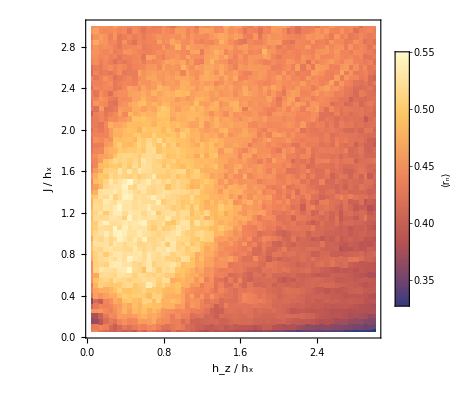

```mathematica
fontSize=18;
fig=
ListDensityPlot[MeanLevelSpacingRatioData,
InterpolationOrder->0,
ColorFunction->Automatic,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"}]
```

## Export data and figure

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_ja/mean_level_spacing_ratio.csv",Prepend[MeanLevelSpacingRatioData,{"h_z/h_x","J/h_x","<r_n>"}],"CSV"]
```

/home/jadeleon/Documents/quantum_chaotic_channels/numerica_ja/mean_level_spacing_ratio.csv

```mathematica
Export["/home/jadeleon/Documents/quantum_chaotic_channels/mean_level_spacing_ratio.png",fig,"PNG",ImageResolution->300]
```

/home/jadeleon/Documents/quantum_chaotic_channels/mean_level_spacing_ratio.png